## Matrix Element calculation (including time evolution)

```mathematica
Clear[ω,ωt,t]
```

```mathematica
L =3.*10^-7; Lstep =1.*10^-8; LN = 2.*L/Lstep + 1.;nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
Uprop[x_,xt_,t_,ωt_]:= ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)]
deltak = 2 Pi/(455 10^-9)//N
ψ[x_, n_, ω_]:= 1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]
ψf[xt_, nt_, ωt_]:= 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]
```

1.38092×10^7

```mathematica
omega[3]
omega[4]
```

```mathematica
2*52564.18722654877
```

105128.

```mathematica
2 Pi/(30 10^-6)//N
```

209440.

```mathematica
2*96487.56959133178
```

192975.

```mathematica
omega[3],omega[5], (1/g35)
```

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

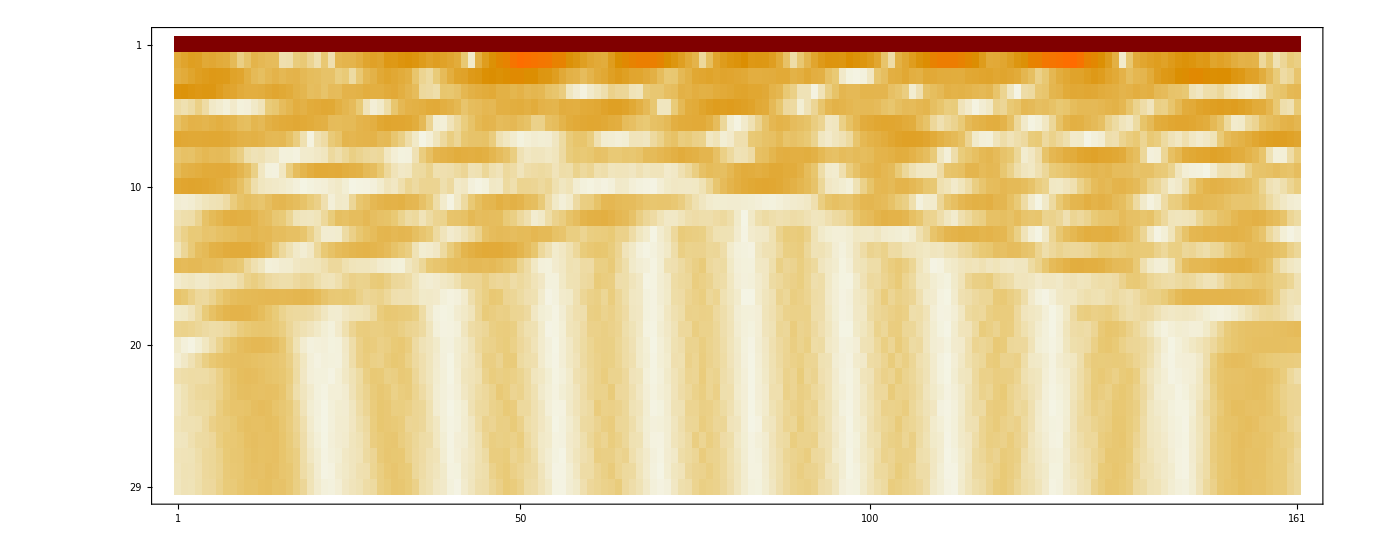

```mathematica
L =0.4*10^-6; Lstep =0.05*10^-7; LN = 2*L/Lstep + 1;
psi[t_, xt_,ω_,ωt_, n_] :=  Lstep*Sum[ψ[x, n, ω]*  Uprop[x,xt,t,ωt],{x,-L,L,Lstep}]
Monitor[evolmat = Table[Abs[psi[t, xt,omega[3],omega[5]/2, 9]]^2,{t,0,2000 10^-9, 70 10^-9},{xt, -L, L, Lstep}];,{(t/(400 10^-9))//N,(xt/L)}]
MatrixPlot[evolmat]
```

```mathematica
nmax = 19.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.8*10^-6; Lstep =0.2*10^-7; LN = 2*L/Lstep + 1;
deltak = 2 Pi/(455 10^-9)//N;
```

```mathematica
UPn[ω_, ωt_,n_, nt_, t_] := Lstep^2 *Sum[ 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]
```

$Aborted

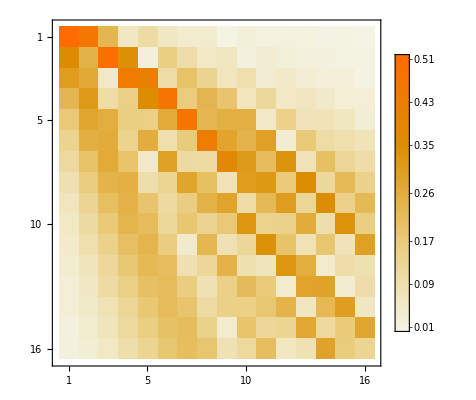

```mathematica
Monitor[ω = omega[1]; ωt=omega[2]; t= 10^-5;uma = Table[Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

## Calculate matrix elements for all segments (Are the decay times of the order of typical ωt? Here: assumed much smaller)

```mathematica
(*from LambDickeParams_Singe.py @532nm and @10**7 lattice beam intensity *)
(*levels=["6s 2 S 1/2","7p 2 P ?3/2","7s 2 S 1/2","6p 2 P ?1/2","6p 2 P ?3/2","5d 2 D 3/2","5d 2 D 5/2"]*)
(*decays=[l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34]*)
omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};
etas = {0.697646827167697,0.14448683087878345,0.17095247621856766,0.35533728030290285,0.10383570605450117,0.3729352538139725,0.06952852571696208,0.07198024772090308,0.19467123685222815,0.21390857630773225,0.23003214721947357};
l21=455.5*10^-9;
l23=2931.8*10^-9;
l35=1469.9*10^-9;
l41=894.3*10^-9;
l64=3011.1*10^-9;
l51=852.1*10^-9;
l65=3614.1*10^-9;
l75=3491*10^-9;
l27=1360.6*10^-9;
l26=1342.8*10^-9;
l34=1359.2*10^-9;
decays={l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34};
g23=4.05*10^6;
g34=6.23*10^6;
g35=11.4*10^6;
g41=28.6*10^6;
g26=0.13*10^6;
g27=1.10*10^6;
g75=0.78*10^6;
g65=0.11*10^6;
g51=32.8*10^6;
g64=0.91*10^6;
g21=1.84*10^6;
gammas={g21,g23,g35,g41,g64,g51,g65,g75,g27,g26,g34};
omega[n_]:= omegas[[n]]/1.01
eta[n_]:= etas[[n]]
nmax = 10.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.6*10^-6; Lstep =0.09*10^-7; LN = 2*L/Lstep + 1;deltak = 2 Pi/(455 10^-9)//N;
```

```mathematica
Clear[t]
```

```mathematica
(*IntU[ω_,ωt_,τ_]:= Monitor[tstart = τ/10;tstop = 3*τ //N; tstep =(tstop/5)//N;*)
IntU[ω_,ωt_,τ_]:= Monitor[tstart =2.5 10^6;tstop = 2.5 10^-6 //N; tstep =τ//N; t = tstart;uma = Table[
Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}] ,{n,nt,t//N}];(*Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}] Exp[-t/τ]/τ,{t,tstart, tstop, tstep}],{n,nt,t//N}]*)
Drw[n_,nt_, η_, θ_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2];
IntDr[η_]:= Table[1/(2 Pi /(Pi/100.5))Sum[Abs[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2]]^2,{θ,0, 2 Pi, Pi/100.5}],{n,0.,nmax},{nt,0.,nmax}];
IntD[η_]:= Table[Abs[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  1)^2]Exp[-(η  1)^2/2]]^2,{n,0.,nmax},{nt,0.,nmax}];
```

```mathematica
omega[3]
omega[5]
```

52564.2

149379.

```mathematica
test
```

{{0.558347,0.374514,0.0106352,0.0356718,0.0143558,0.00132893,0.00412232,0.0000146236,0.000753778,0.0000848207,0.000100033},{0.133104,0.128536,0.505486,0.0621729,0.0749598,0.0642512,0.00222804,0.0217753,0.00052531,0.00461827,0.000930431},{0.142307,0.0210008,0.0109409,0.379937,0.132809,0.078982,0.145097,0.000785207,0.0587927,0.003986,0.0143472},{0.0615073,0.138128,0.0203072,0.000227385,0.173942,0.155758,0.0501394,0.213855,0.000368565,0.105791,0.0152075},{0.0466185,0.0673396,0.0573462,0.1287,0.00378754,0.0392394,0.104316,0.0185337,0.221609,0.00619881,0.139096},{0.0232987,0.0898161,0.0185086,0.00832741,0.199122,0.0319553,0.000630765,0.0286253,0.00323293,0.160034,0.0161105},{0.015416,0.0516254,0.0802531,0.00280182,0.0000109942,0.167038,0.0855348,0.00475603,0.000448654,0.000246481,0.0713403},{0.0081215,0.0462964,0.047968,0.0374626,0.053389,0.000033063,0.084067,0.118676,0.00739264,0.0377788,0.000533712},{0.00501136,0.0276385,0.0668064,0.0163445,0.00672123,0.116631,0.00712923,0.0220333,0.0951486,0.00287884,0.0936325},{0.00269658,0.0208196,0.0437679,0.0570555,0.000233603,5.63776×10^-7,0.130721,0.0383412,0.0011802,0.0372215,0.00010629},{0.00159652,0.0124835,0.0423038,0.0381657,0.0280633,0.0267229,0.000296438,0.0917102,0.0829026,0.000641394,0.00110564}}

```mathematica
MatrixPlot[IntD[0.7], PlotLegends -> True] (*test*)
```

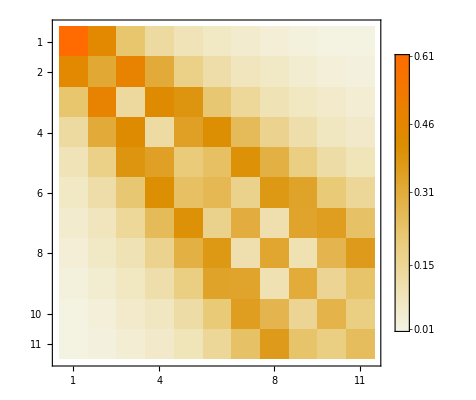
```mathematica
-Graphics-0
```

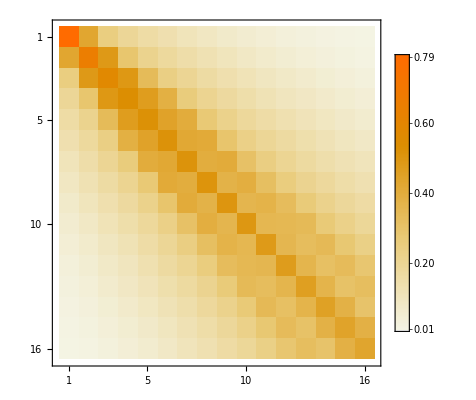

```mathematica
MatrixPlot[IntDr[0.7], PlotLegends -> True] (*test*)
```

Power::indet: Indeterminate expression (0.+0. ⅈ)^0 encountered.

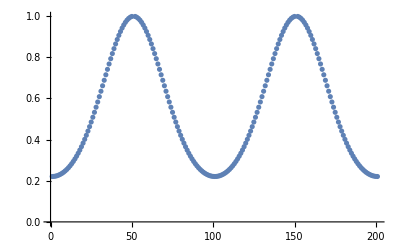

```mathematica
ListPlot[Table[Abs[Drw[15,15, 0.2, θ]]^2,{θ,0, 2 Pi, Pi/100}]]
```

```mathematica
0
```

```mathematica
U12= IntU[omega[1],omega[2], (1/g21) //N];
U23 = IntU[omega[2],omega[3], (1/g23) //N];
U35 = IntU[omega[3],omega[5], (1/g35) //N];
U41 = IntU[omega[4],omega[1], (1/g41) //N];
U64 = IntU[omega[6],omega[4], (1/g64) //N];
U51 = IntU[omega[5],omega[1], (1/g51) //N];
U65 = IntU[omega[6],omega[5], (1/g65) //N];
U75 = IntU[omega[7],omega[5], (1/g75) //N];
U27 = IntU[omega[2],omega[7], (1/g27) //N];
U26 = IntU[omega[2],omega[6], (1/g26) //N];
U34 = IntU[omega[3],omega[4], (1/g34) //N];
```

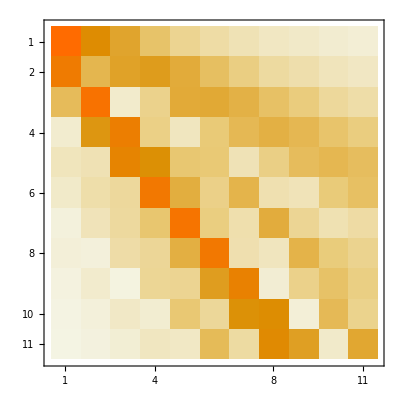
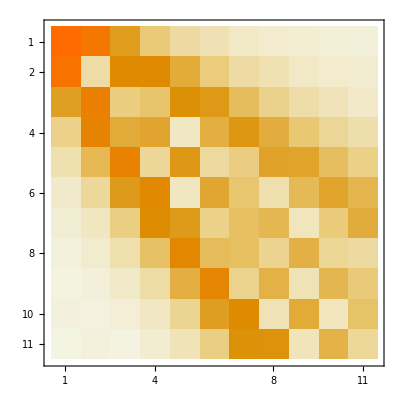
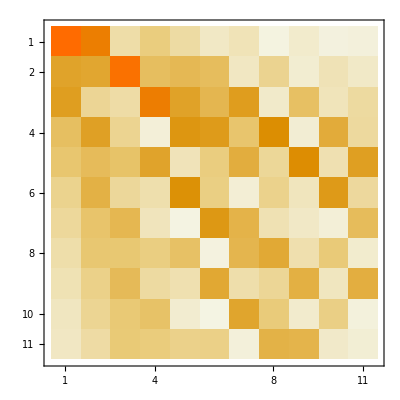
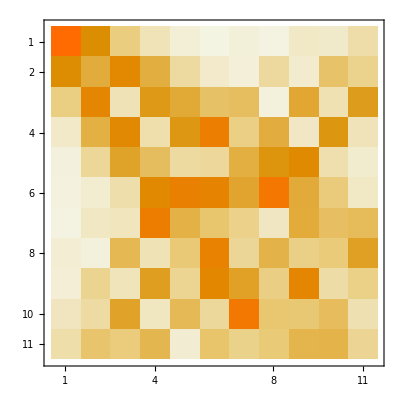
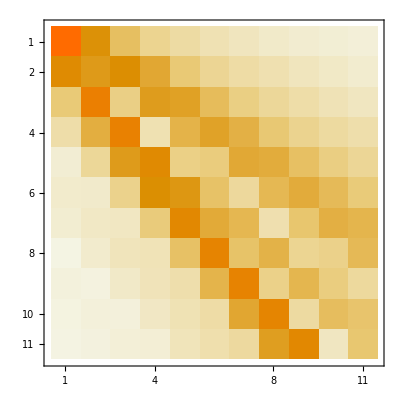
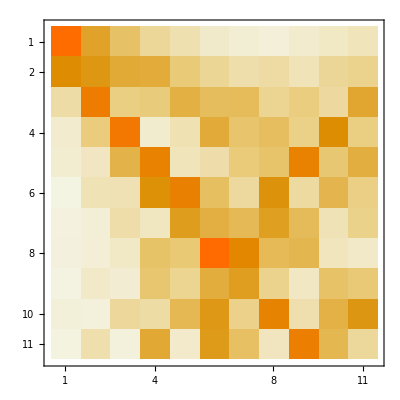
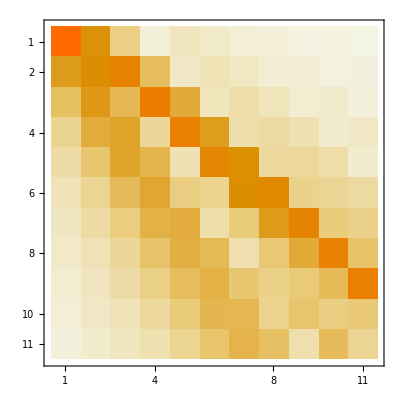
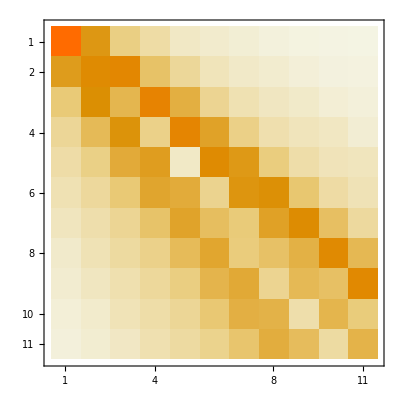

```mathematica
{MatrixPlot[U12],MatrixPlot[U23],MatrixPlot[U35],MatrixPlot[U41],MatrixPlot[U64],MatrixPlot[U51],MatrixPlot[U65],MatrixPlot[U75],MatrixPlot[U27],MatrixPlot[U26],MatrixPlot[U34]}
```

```mathematica
(*omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};*)
```

```mathematica
D12 = IntD[eta[1]];
D21 = IntDr[eta[1]];
D23 = IntDr [eta[2]];
D35 = IntDr[eta[3]];
D41 = IntDr[eta[4]];
D64 = IntDr[eta[5]];
D51 = IntDr[eta[6]];
D65 = IntDr[eta[7]];
D75 = IntDr[eta[8]];
D27 = IntDr[eta[9]];
{{D26 = IntDr[eta[10]];}, {D34 = IntDr[eta[11]];}}
```

{{Null},{Null}}

```mathematica
pathA = D41.U34.D34.U23.D23.U12.D12; (*7p3/2 -> 7s1/2 -> 6p1/2-> 6s1/2*)
pathB = D51.U35.D35.U23.D23.U12.D12;(*7p3/2 -> 7s1/2 -> 6p3/2-> 6s1/2*)
pathC = D51.U65.D65.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p3/2-> 6s1/2*)
pathD = D41.U64.D64.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
pathE = D51.U75.D75.U27.D27.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
pathF = D21.U12.D12;

paths ={pathA, pathB, pathC, pathD, pathE, pathF};(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
```

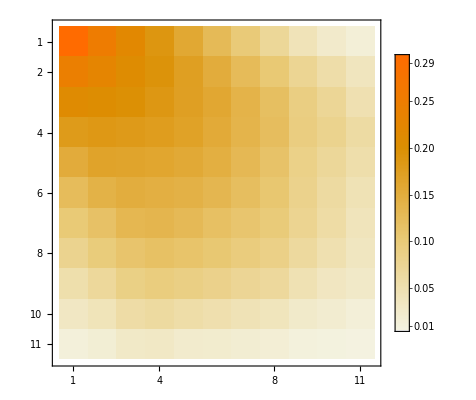

```mathematica
MatrixPlot[pathE, PlotLegends -> True]
```

```mathematica
pathA[[1,All]]
```

{0.257185,0.190051,0.13969,0.104527,0.077727,0.0575355,0.0427835,0.0315194,0.0224633,0.0172757,0.0132948}

```mathematica
Table[pathA[[1,All]][[ra]] ra,{ra,1,Length[pathA[[1,All]]]}]
```

{0.258621,0.381394,0.419753,0.417978,0.38729,0.3415,0.292263,0.245834,0.205868,0.173767,0.146911,0.120546,0.0935371,0.0696522,0.0491078,0.0304102}

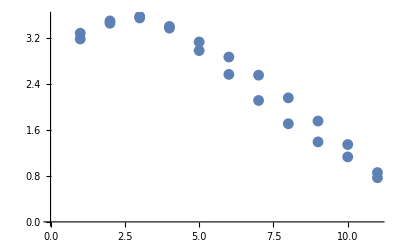

```mathematica
plotpath[pa_]:=ListPlot[Table[Sum[paths[[pa]][[r,All]][[ra]] ra,{ra,1,Length[paths[[pa]][[r,All]]]}],{r,1,Length[paths[[pa]][[1,All]]]}]]
Show[{plotpath[1],plotpath[4]}]
```

```mathematica
pathTot = 0.201004*pathA +0.3678 pathB +0.001969 pathC + 0.016289pathD + 0.154494pathE + 0.258427 pathF
```

{{0.29623,0.20525,0.141707,0.0999573,0.0709534,0.0507035,0.0365851,0.0262862,0.0183431,0.0135643,0.0100276},{0.200791,0.160751,0.128976,0.101288,0.0817176,0.0662294,0.0526429,0.0401647,0.0284426,0.0215828,0.0163513},{0.136754,0.12365,0.115409,0.10049,0.0826478,0.0680419,0.056373,0.0463774,0.0347693,0.0277874,0.0217733},{0.0917573,0.101154,0.096358,0.0907963,0.0806285,0.0673373,0.0553257,0.0450259,0.0335422,0.0282711,0.0231747},{0.0624668,0.0817577,0.080525,0.0775929,0.0724401,0.0644196,0.0536425,0.0435312,0.0306507,0.025019,0.020814},{0.0445644,0.0626596,0.0684267,0.0654066,0.0628035,0.0580504,0.0502182,0.0412636,0.029751,0.0233767,0.0184249},{0.0332846,0.0474088,0.0566241,0.0566272,0.0542506,0.0506649,0.0467511,0.0392744,0.0283332,0.0230239,0.0181064},{0.0257605,0.0359854,0.0457761,0.0488069,0.04674,0.0451211,0.0400688,0.0373405,0.0279539,0.0222691,0.0177057},{0.0202674,0.0273093,0.0359759,0.0400872,0.0401544,0.036817,0.0346797,0.0312267,0.0249514,0.0211528,0.0165857},{0.0153462,0.0200903,0.0265272,0.0313102,0.0319637,0.0299435,0.0268418,0.0262224,0.0198845,0.0181597,0.0150679},{0.0098469,0.0127597,0.0168113,0.0214581,0.0226165,0.0223485,0.0186293,0.0198362,0.0154316,0.0136055,0.0124177}}

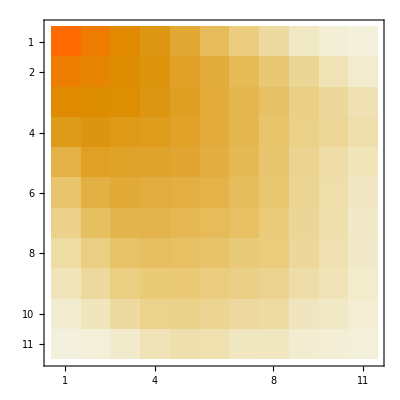

```mathematica
MatrixPlot[pathTot]
```

```mathematica
paths ={pathA, pathB, pathC, pathD, pathE, pathF, pathTot};
```

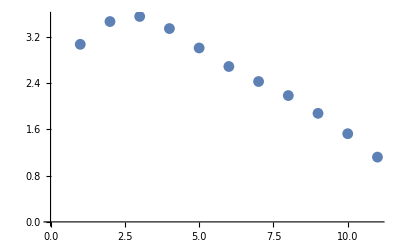

```mathematica
Show[{plotpath[7]}]
```